i n o^2 R t^2

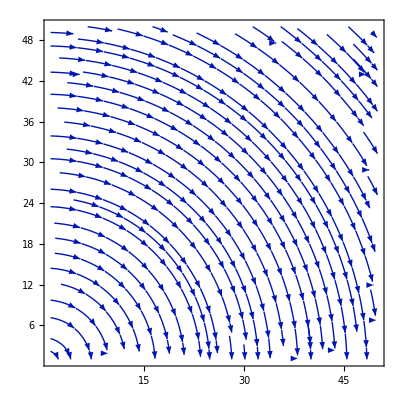

```mathematica
Rotation

w={0,0,1};
a=1;
X={x,y,0};
r=√(x^2+y^2);
StreamPlot[{-Dot[Cross[w,X],{1,0,0}]*(a/r)^3,-Dot[Cross[w,X],{0,1,0}]*(a/r)^3},{x,1,50},{y,1,50}]
```

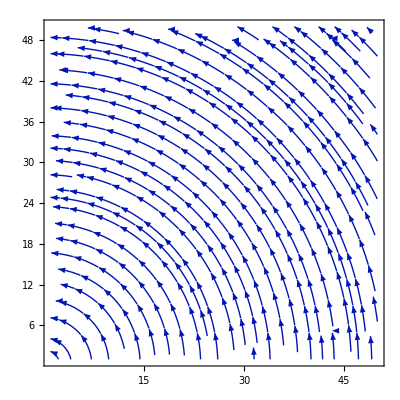

```mathematica
w={0,0,1};
a=1;
X={x,y,0};
r= √(x^2+y^2);
StreamPlot[{Dot[Cross[w,X],{1,0,0}]* (a/r)^3,Dot[Cross[w,X],{0,1,0}]* (a/r)^3},{x,1,50},{y,1,50}]
```

#### Translation Pressure

```mathematica
λ=1;
U={0,1,0};
X={x,y,0};
r= √(x^2+y^2);
ContourPlot[{Dot[U,X]* λ/r^3,0},{x,-5,5},{y,-5,5}]
```

-Graphics-

```mathematica
a=1;
U={0,1};
Subscript[δ, ij]={{1,0},{0,1}};
XX= {{x x,x y},{y x,y y}};
r=√(x^2+ y^2);
{{u,v}}= Dot[{(-3*a)/4(Subscript[δ, ij]/r+XX/r^3)-(3*a^3)/4(Subscript[δ, ij]/(3*r^3)-XX/r^5)},U]
```

{{(3 x y)/(4 (x^2+y^2)^(5/2))-(3 x y)/(4 (x^2+y^2)^(3/2)),-3/4 (-y^2/((x^2+y^2)^(5/2))+1/(3 (x^2+y^2)^(3/2)))-3/4 (y^2/((x^2+y^2)^(3/2))+1/(√(x^2+y^2)))}}

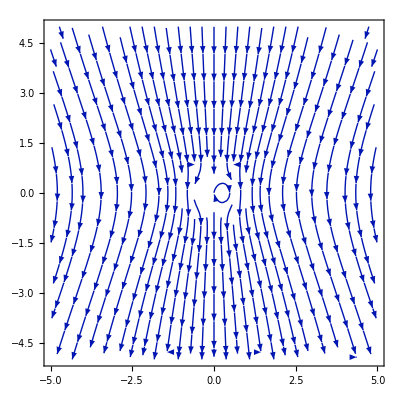

```mathematica
StreamPlot[{u,v},{x,-5,5},{y,-5,5}]
```

Disturbance Velocity Field  (Disturbance streamlines for a translating sphere) .

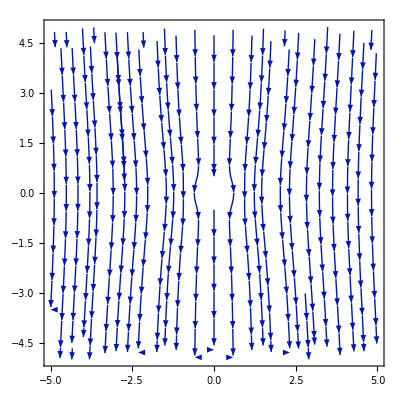

```mathematica
StreamPlot[{u,v-1},{x,-5,5},{y,-5,5}]
```

full streamlines for a particle fixed in uniform stream

```mathematica
Straining
Pressure
```

```mathematica
Clear[μ,x,y,a,r]
```

-(10 x y)/((x^2+y^2)^(5/2))

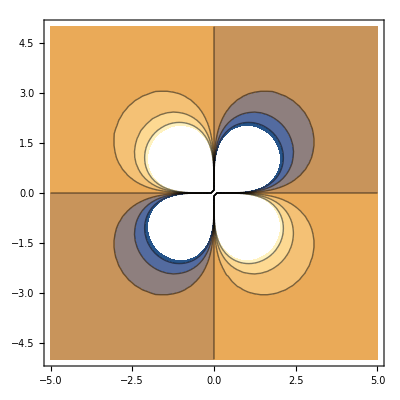

```mathematica
μ=1;
r=√(x^2+y^2);
a=1;
X={x,0};
Y = {0,y};
Subscript[E, ij]={{1,2},{2,3}};
p=(-5*μ*a^3*Dot[Dot[X,Subscript[E, ij]],Y])/r^5
ContourPlot[p,{x,-5,5},{y,-5,5}]
```

```mathematica
Clear[Subscript[E, jk],r,a,X,Y,Z]
```

Clear::ssym: ⅇ_jk is not a symbol or a string.

```mathematica
Velocity Field
```

```mathematica
Subscript[E, jk]={{1,1,1},{1,1,1},{1,1,1}};
a=1;
r=√(x^2+y^2+z^2);
Subscript[δ, ij]={{1,0,0},{0,1,0},{0,0,1}};
X={x,0,0};
Y={0,y,0};
Z={0,0,z};

{u,v,w}=(-5*a^3)/2*(X*Dot[Dot[Y,Subscript[E, jk]],Z])/r^5-a^5/2*((Dot[Dot[Subscript[δ, ij],Subscript[E, jk]],Z]+Dot[Dot[Subscript[δ, ij],Subscript[E, jk]],Y])/r^5- (X*Dot[Dot[Y,Subscript[E, jk]],Z])/r^7)
```

{-(5 x y z)/(2 (x^2+y^2+z^2)^(5/2))+1/2 ((x y z)/((x^2+y^2+z^2)^(7/2))-(y+z)/((x^2+y^2+z^2)^(5/2))),-(y+z)/(2 (x^2+y^2+z^2)^(5/2)),-(y+z)/(2 (x^2+y^2+z^2)^(5/2))}

1.5

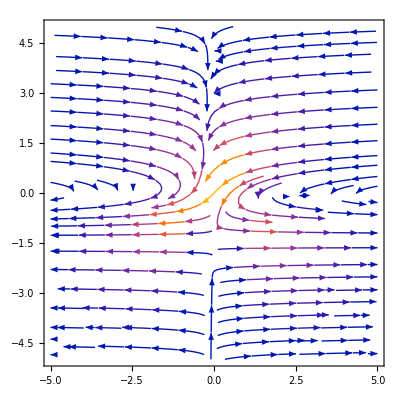

```mathematica
z=1.5
StreamPlot[{u,v},{x,-5,5},{y,-5,5}]
```

```mathematica
Translation Coded Differently
```

```mathematica
Clear[U,X]
```

```mathematica
U={Subscript[U, 1],0,0};
X={x,y,z};
r=√(x^2+y^2=z^2);
u=(3 a)/4(U/r+((U.X)X)/r^3)+a^3/4(U/r^3-(3(U.X)X)/r^5)
p=(3μ a)/2((U.X)/r^3)
```

```mathematica
Subscript[U, S]=(3 a)/4(U/r+((U.X)X)/r^3)
(*u-> Stokes Flow Velocity Field
 p-> Pressure Field
   Subscript[U, S]-> Stokeslet Velocity Field*)
ux=u[1];uy=u[2];uz=u[3];
Subscript[U, S] x=Subscript[U, S]⟦1⟧;Subscript[U, S] y=Subscript[U, S]⟦2⟧;Subscript[U, S] z=Subscript[U, S]⟦3⟧;
Subscript[U, S]//MatrixForm
```

3/4 a (U/r+(X U.X)/r^3)

Set::write: Tag Times in 1/4 x (3 a (U/r+(X U.X)/r^3)) is Protected.

Set::write: Tag Times in 1/4 y (3 a (U/r+(X U.X)/r^3)) is Protected.

Set::write: Tag Times in 1/4 z (3 a (U/r+(X U.X)/r^3)) is Protected.

General::stop: Further output of Set::write will be suppressed during this calculation.

3/4 a (U/r+(X U.X)/r^3)